## Fixed points

Try to model exactly the solution for two cells
v1: used to create multiple plots together. Less cleaned up.

```mathematica
Clear["Global`*"];
```

```mathematica
S[x_]:= Coff +(Con-Coff)*x;
g[x1_,x2_]:= S[x1] + fd*S[x2];
RSolve[{x1[t+1] == g[x1[t], x2[t]]^n/(k^n+g[x1[t], x2[t]]^n),x2[t+1] == g[x2[t], x1[t]]^n/(k^n+g[x2[t], x1[t]]^n), x1[0]==x1i, x2[0]==x2i} /. {n-> 1}, {x1[t],x2[t]},t]
```

RSolve[{x1[1+t]==(Coff+(-Coff+Con) x1[t]+fd (Coff+(-Coff+Con) x2[t]))/(Coff+k+(-Coff+Con) x1[t]+fd (Coff+(-Coff+Con) x2[t])),x2[1+t]==(Coff+fd (Coff+(-Coff+Con) x1[t])+(-Coff+Con) x2[t])/(Coff+k+fd (Coff+(-Coff+Con) x1[t])+(-Coff+Con) x2[t]),x1[0]==x1i,x2[0]==x2i},{x1[t],x2[t]},t]

Typical value of f(d):

```mathematica
fdval = Exp[R-a0]/a0 Sinh[R] /. {R-> 0.1, a0-> 0.5}
```

0.134288

### Fixed points (exact)

For n = 2 we can obtain exact solutions from the solution of the cubic equation.

```mathematica
Solve[{0== g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,0 == g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2} /. {n-> 2}, {x1,x2}]
```

$Aborted

```mathematica
red =Reduce[(0== g[x1, x2]^n/(k^n+g[x1, x2]^n) -x1&&0 == g[x2, x1]^n/(k^n+g[x2, x1]^n) -x2)/. {n-> 2}, {x1,x2}]
```

$Aborted

```mathematica
For[i=1, i≤ Length[red],i++, Print[red[[i]] ] ]
```

Con==0&&Coff==0&&-k+fd^2 k≠0

fd==-1&&Coff==Con&&k≠0

fd==1&&Con==0&&Coff==0&&k≠0

(fd==-1||fd==1)&&Coff-Con≠0&&x2==(Coff+Coff fd-Coff fd x1+Con fd x1)/(Coff-Con)&&k≠0

(Coff-Con) (-1+fd^2)≠0&&x1==Coff/(Coff-Con)&&x2==(Coff+Coff fd-Coff fd x1+Con fd x1)/(Coff-Con)&&k≠0

Special case X1 = X2

```mathematica
Solve[{0== g[x, x]^n/(k^n+g[x, x]^n)-x} /. {n-> 2}, {x}]
```

$Aborted

Rewrite equation into
 -(C_on-1)^2 X^3+[(C_on-1)^2 -2 (C_on-1)]X^2 + [2(C_on-1) - 1 - K^2/((1 + f(d))^2)]X + 1 =0

Δ = 18 a b c d - 4 b^3 d + b^2 c^2 - 4 a c^3 - 27 a^2 d^2;
Δ > 0: three distinct roots

```mathematica
a=  -(Con-1)^2;
b = (Con-1)^2 -2 (Con-1);
c =  2(Con-1) - 1 - k^2/((1 + fd)^2);
d = 1;
Δ = 18 a b c d - 4 b^3 d + b^2 c^2 - 4 a c^3 - 27 a^2 d^2;
Apart[Δ]
```

-(4 (-1+Con)^2 Con^3 k^2)/(1+fd)^2+((-1+Con)^2 (-27+18 Con+Con^2) k^4)/(1+fd)^4-(4 (-1+Con)^2 k^6)/(1+fd)^6

```mathematica
Solve[Δ == 0, fd, Reals]
```

{{fd→ConditionalExpression[Root[4 Con^3+27 k^2-18 Con k^2-Con^2 k^2+4 k^4+(16 Con^3+54 k^2-36 Con k^2-2 Con^2 k^2) #1+(24 Con^3+27 k^2-18 Con k^2-Con^2 k^2) #1^2+16 Con^3 #1^3+4 Con^3 #1^4&,1],Con>9||Con<0]},{fd→ConditionalExpression[Root[4 Con^3+27 k^2-18 Con k^2-Con^2 k^2+4 k^4+(16 Con^3+54 k^2-36 Con k^2-2 Con^2 k^2) #1+(24 Con^3+27 k^2-18 Con k^2-Con^2 k^2) #1^2+16 Con^3 #1^3+4 Con^3 #1^4&,2],Con>9||Con<0]},{fd→ConditionalExpression[Root[4 Con^3+27 k^2-18 Con k^2-Con^2 k^2+4 k^4+(16 Con^3+54 k^2-36 Con k^2-2 Con^2 k^2) #1+(24 Con^3+27 k^2-18 Con k^2-Con^2 k^2) #1^2+16 Con^3 #1^3+4 Con^3 #1^4&,3],Con>9]},{fd→ConditionalExpression[Root[4 Con^3+27 k^2-18 Con k^2-Con^2 k^2+4 k^4+(16 Con^3+54 k^2-36 Con k^2-2 Con^2 k^2) #1+(24 Con^3+27 k^2-18 Con k^2-Con^2 k^2) #1^2+16 Con^3 #1^3+4 Con^3 #1^4&,4],Con>9]}}

Note that Δ is a quintic equation in C_on, therefore it is not easy to find the roots of Δ=0 which gives the range where we have three real solutions.

### Fixed points (numerical)

If there exists a solution, it appears to be unique. However, it seems that Mathematica is only able to find solutions for specific values of n (e.g. n=1, 2, 1.5, 1.2)

Try out solution

```mathematica
params = {k-> 10, Coff-> 1, Con-> 15, fd-> fdval, n-> 1.8};
NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals} /. params, {x1,x2}]
```

{{x1→0.0472433,x2→0.0472433}}

Plot against Con

```mathematica
params = {k-> 10, Coff-> 1,fd->fdval};
del = 0.2;
nsol=Table[
NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals, 0≤x1≤1, 0≤x2≤1 } /. params /.{n-> 1, Con-> c}, {x1,x2}],{c,1,30,del}];
nsol2=Table[
NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals, 0≤x1≤1, 0≤x2≤1} /. params /.{n-> 1.5,  Con-> c}, {x1,x2}],{c,1,30,del}];
nsol3=Table[
NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals, 0≤x1≤1, 0≤x2≤1} /. params /.{n-> 2,  Con-> c}, {x1,x2}],{c,1,30,del}];
```

Process data to get all solutions

```mathematica
lvals3=Length/@(x1/.nsol3);
t=Table[ ConstantArray[1+(i-1)*del, lvals3[[i]]], {i, 1, Length[lvals3]}] ;
pvals3=Flatten[Transpose/@Transpose[{t,x1/.nsol3}], {1,2}];

lvals2=Length/@(x1/.nsol2);
t=Table[ ConstantArray[1+(i-1)*del, lvals2[[i]]], {i, 1, Length[lvals2]}] ;
pvals2=Flatten[Transpose/@Transpose[{t,x1/.nsol2}], {1,2}];

lvals1=Length/@(x1/.nsol);
t=Table[ ConstantArray[1+(i-1)*del, lvals1[[i]]], {i, 1, Length[lvals1]}] ;
pvals1=Flatten[Transpose/@Transpose[{t,x1/.nsol}], {1,2}];
```

Compare with Δ of cubic equation (n=2)

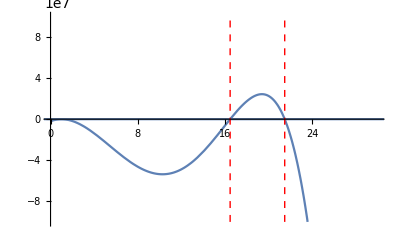

```mathematica
sol = NSolve[(Δ/.{k-> 10, Coff-> 1,fd->fdval}) ==0 && Con>1, Con];
linestyle={Red, Thick, Dashed};
line1 = Line[{{Con/.sol[[1]], -10^8},{Con/.sol[[1]],10^8}}];
line2 = Line[{{Con/.sol[[2]],-10^8},{Con/.sol[[2]],10^8}}];
p0a = Plot[Δ/.{k-> 10, Coff-> 1,fd->fdval}, {Con, 0, 30}, PlotRange-> {{0, 30}, {-10^8, 10^8}}, Epilog->{Directive[linestyle],line1,line2}];
Show[p0a, p0b]
```

Plot together

```mathematica
linestyle={Yellow, Thick, Dashed};
line1 = Line[{{Con/.sol[[1]], 0},{Con/.sol[[1]],1}}];
line2 = Line[{{Con/.sol[[2]],0},{Con/.sol[[2]],1}}];
```

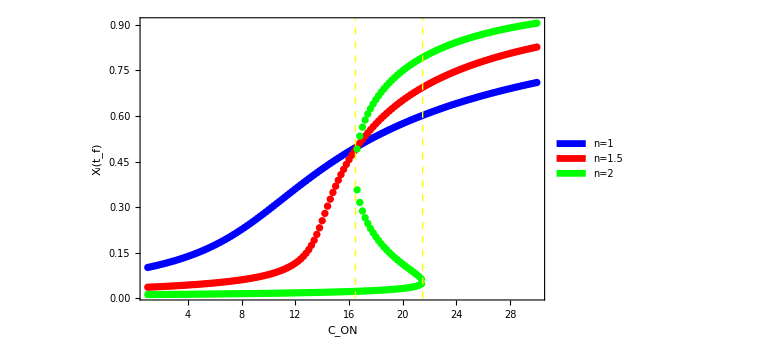

```mathematica
fstyle = Style[#,16] & ;
l1 = Placed[SwatchLegend[fstyle/@{"n=1"}, LegendMarkerSize->10],Above]; 
l2 = Placed[SwatchLegend[fstyle/@{"n=1.5"}, LegendMarkerSize->10],Above] ;
l3= Placed[SwatchLegend[fstyle/@{"n=2"}, LegendMarkerSize->10],Above] ;
p1=ListPlot[pvals1, PlotStyle-> {Blue}, AxesLabel-> {"C_ON", "X_i(t_f)"}, PlotLegends-> l1 ];
p2=ListPlot[pvals2, PlotStyle-> {Red},AxesLabel-> {"C_ON", "X_i(t_f)"}, PlotLegends->  l2];
p3=ListPlot[pvals3, PlotStyle-> {Green},AxesLabel-> {"C_ON", "X_i(t_f)"}, PlotLegends->  l3];
fig2=Show[p1,p2,p3,ImageSize-> Large,BaseStyle-> {FontSize-> 20}, Frame-> True, FrameLabel-> {"C_ON", "X_i(t_f)"}, PlotRange-> All,Epilog->{Directive[linestyle],line1,line2}]
```

Export figure

```mathematica
name = "steady_state_vs_Con_k_10_Coff_1_fd_0p13_fN_1p5_n_var.pdf";
fname = FileNameJoin[{NotebookDirectory[], "finite_Hill_two_cells", name}];
(*Export[fname,fig2]*)
```

H:\My Documents\Multicellular automaton\Mathematica calculations\finite_Hill_homogenisation\steady_state_vs_Con_k_10_Coff_1_fd_0p13_fN_1p5_n_var.pdf

### Fixed points part 2

```mathematica
params = {k-> 10, Coff-> 1,fd-> fdval};
del = 0.5;
nsol4=Table[
NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals, 0≤x1≤1, 0≤x2≤1 } /. params /.{n-> 1.8, Con-> c}, {x1,x2}],{c,1,30,del}];
```

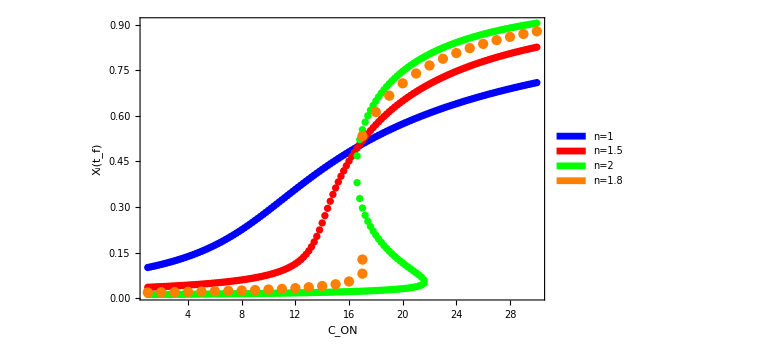

```mathematica
l4= Placed[SwatchLegend[fstyle/@{"n=1.8"}, LegendMarkerSize->10],Above];
lvals4=Length/@(x1/.nsol4);
t=Table[ ConstantArray[1+(i-1)*del, lvals4[[i]]], {i, 1, Length[lvals4]}] ;
pvals4=Flatten[Transpose/@Transpose[{t,x1/.nsol4}], {1,2}];
p4=ListPlot[pvals4, PlotStyle-> {Orange}, AxesLabel-> {"C_ON", "X_i(t_f)"}, PlotLegends-> l4];
fig4=Show[p1,p2,p3,p4, BaseStyle-> {FontSize-> 20}, ImageSize-> Large,Frame->True, FrameLabel-> {"C_ON", "X_i(t_f)"}, PlotRange-> All]
```

```mathematica
params = {k-> 10, Coff-> 1,fd-> 0.13,fN-> 1.5};
del = 0.5;
nsol5=Table[
NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals, 0≤x1≤1, 0≤x2≤1 } /. params /.{n-> 1.7, Con-> c}, {x1,x2}],{c,1,30,del}];
l5= Placed[SwatchLegend[fstyle/@{"n=1.7"}, LegendMarkerSize->10],Above];
lvals5=Length/@(x1/.nsol5);
t=Table[ ConstantArray[1+(i-1)*del, lvals5[[i]]], {i, 1, Length[lvals5]}] ;
pvals5=Flatten[Transpose/@Transpose[{t,x1/.nsol5}], {1,2}];
```

$Aborted

ReplaceAll::reps: {nsol5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {nsol5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Transpose::nmtx: The first two levels of {{{}, {}}, x1/. nsol5} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

```mathematica
p5=ListPlot[pvals4, PlotStyle-> {Purple}, AxesLabel-> {"C_ON", "X_i(t_f)"}, PlotLegends-> l5];
fig4=Show[p1,p2,p3,p4, p5,BaseStyle-> {FontSize-> 20}, ImageSize-> Large,Frame->True, FrameLabel-> {"C_ON", "X_i(t_f)"}, PlotRange-> All]
```

Export figure

```mathematica
name = "steady_state_vs_Con_k_10_Coff_1_fd_0p13_fN_1p5_n1p8.pdf";
fname = FileNameJoin[{NotebookDirectory[], "finite_Hill_homogenisation", name}];
(*Export[fname,fig4]*)
```

H:\My Documents\Multicellular automaton\Mathematica calculations\finite_Hill_homogenisation\steady_state_vs_Con_k_10_Coff_1_fd_0p13_fN_1p5_n1p8.pdf

Plot against K

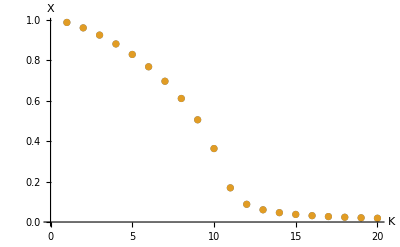

```mathematica
nsol=Table[
First@NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals} /. {k-> c, Coff-> 1, Con->15, fd-> 0.13,fN-> 1.5, n-> 1.5}, {x1,x2}], {c,1,20}];
ListPlot[{x1/.nsol, x2/.nsol}, AxesLabel-> {"K", "X"}]
```

Plot against fN

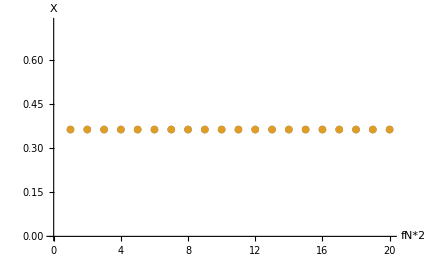

```mathematica
nsol=Table[
First@NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals} /. {k-> 10, Coff-> 1, Con->15, fd-> 0.13,fN->c, n-> 1.5}, {x1,x2}], {c,0.5,10,0.5}];
ListPlot[{x1/.nsol, x2/.nsol}, AxesLabel-> {"fN*2", "X"}]
```

Changing n is problematic. 
Note that for n=1 there might be negative solutions. First does not give correct solution.

```mathematica
nsol=Table[
First@NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals} /. {k-> 10, Coff-> 1, Con->15, fd-> 0.13,fN->1.5, n-> c}, {x1,x2}], {c,1,2,1/10}];
ListPlot[{x1/.nsol, x2/.nsol}, AxesLabel-> {"20 n", "X"}]
```

First::nofirst: {} has a length of zero and no first element.

General::stop: Further output of First :: nofirst will be suppressed during this calculation.

ReplaceAll::rmix: Elements of {{x1 → 0.362135, x2 → -0.287135}, First[{}], First[{}], First[{}], First[{}], First[{}], First[{}], First[{}], First[{}], First[{}], {x1 → 0.0208802, x2 → 0.0208802}} are a mixture of lists and nonlists.

-Graphics-

```mathematica
nsol
```

{{x1→-0.352912,x2→0.245769},First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],{x1→0.596174,x2→0.596174}}

```mathematica
NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals} /. {k-> 10, Coff-> 1, Con->15, fd-> 0.13,fN->1.5, n->1.2}, {x1,x2}]
```

{{x1→0.432324,x2→0.432324}}

### Fixed point properties

Calculate Jacobian matrix. General expression for eigenvalues is not useful.

```mathematica
J=FullSimplify/@{{D[g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,x1],D[g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,x2]},{ D[g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2,x1],D[g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2,x2]}};
J  // MatrixForm
```

(-1-((Coff-Con) k^n n (Coff (1+fd-x1-fd x2)+Con (x1+fd x2))^(-1+n))/((k^n+(Coff (1+fd-x1-fd x2)+Con (x1+fd x2))^n)^2) | -((Coff-Con) fd k^n n (Coff (1+fd-x1-fd x2)+Con (x1+fd x2))^(-1+n))/((k^n+(Coff (1+fd-x1-fd x2)+Con (x1+fd x2))^n)^2)
-((Coff-Con) fd k^n n (Coff (1+fd-fd x1-x2)+Con (fd x1+x2))^(-1+n))/((k^n+(Coff (1+fd-fd x1-x2)+Con (fd x1+x2))^n)^2) | -1-((Coff-Con) k^n n (Coff (1+fd-fd x1-x2)+Con (fd x1+x2))^(-1+n))/((k^n+(Coff (1+fd-fd x1-x2)+Con (fd x1+x2))^n)^2))

Numerically calculate eigenvalues at the fixed points. Verify that they are stable (Re[λ] < 0 for all λ).

```mathematica
params = {k-> 10, Coff-> 1, Con->17, fd-> fdval, n->2};
Jn =FullSimplify[J  /. params];
Jn /. nsol[[2]] // MatrixForm
Table[ Eigenvalues[Jn  /. nsol[[i]]], {i, 1, Length[nsol]}]
```

{{-1+(0.78125 (0.070893+x1+0.134288 x2))/((0.395651+x1^2+x1 (0.141786+0.268575 x2)+(0.0190401+0.0180331 x2) x2)^2),(0.00743753+0.104912 x1+0.0140884 x2)/((0.395651+x1^2+x1 (0.141786+0.268575 x2)+(0.0190401+0.0180331 x2) x2)^2)},{(22.871+43.323 x1+322.614 x2)/((21.9402+1. x1^2+x1 (1.05584+14.8934 x2)+x2 (7.86252+55.4534 x2))^2),-1+(170.314+322.614 x1+2402.41 x2)/((21.9402+1. x1^2+x1 (1.05584+14.8934 x2)+x2 (7.86252+55.4534 x2))^2)}}/.nsol⟦2⟧

{}

Solve for f(x1,x2)=f(x2,x1)

```mathematica
sol=Solve[{g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1 == g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2, n∈ Reals} /. {n-> 2}, x1]
```

{{x1→x2},3,{x1→-(-Coff-2 Coff fd-Coff fd^2+Coff x2-Con x2+Coff fd^2 x2-Con fd^2 x2)/(2 (Coff-Con) fd)+1/2 √((1)^2/((Coff-Con)^2 fd^2)-(Coff^2+32+Con^2 fd^4 x2^2)/((Coff-3)^2 fd^2)+1+(2^1 1)/(3 2 1)+(1)^(1/3)/(3 2^(1/3) (Coff-Con)^4 fd^2))+1/2 √(9+(-(8 (1)^3)/((Coff-Con)^3 fd^3)+(8 (1) (1))/(1^3 fd^3)-(8 (1))/((1)^3 fd^2))/(4 √(5+(1)^(1/3)/(3 2^1 1 fd^2))))}}
 |  |  |  |

```mathematica
Plot[x1 /. sol[[2]] /. params, {x2,0,1}, PlotRange-> All]
```

-Graphics-